## Phasenraum ohne Gaußverbreiterung

```mathematica
γ=1; B1=1; νres=1; c=0.1;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
Plot3D[MzNorm[Φ0,ν],{Φ0,0,20},{ν,-0,2},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->300,Boxed->False,PlotLabel->"Phasenraum ohne Gaußverbreiterung",AxesLabel->{"Normierte Einstrahlintensität","normierte Frequenz","Signal"},LabelStyle->Large]
```

-Graphics3D-

## Phasenraum mit Gaußverbreiterung

```mathematica
γ=1; B1=1; νres=1; c=0.05;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]:=NIntegrate[1/(1+u[ν]^2)(u[ν]^2+Cos[Φ √(1+u[ν]^2)])*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c Φ0)],{Φ,−Infinity,Infinity}];
Plot3D[MzNorm[Φ0,ν],{Φ0,0.1,20},{ν,1,1.5},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->50,Boxed->False,PlotLabel->"Phasenraum mit Gaußverbreiterung",AxesLabel->{"Drehwinkel","normierte Frequenz","Signal"},LabelStyle->Directive[Bold]]
```

## Experimentelle Daten Symmetrisieren

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-minmax.dat", "Table"];
Data=Data[[14;;]];
Manipulate[ListPlot[(Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2), PlotRange->{-1,1}],{{k,0.85},0.001,2},{{l,1.14},1,1.5}]
ExSymData=(Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2)/.{k->0.85,l->1.14};
```

## Theorie nur auf der Resonanzfrequenz

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
Manipulate[Plot[-MzNormSpinDreh[Φ0/γct,c],{Φ0,0.001,7000}, PlotRange->{-1,1}, PlotPoints->10],{{c,0.12},0.001,0.5,0.01},{{γct,230},100,1000}]
```

```mathematica
Plot
```

## Experimentelle Daten

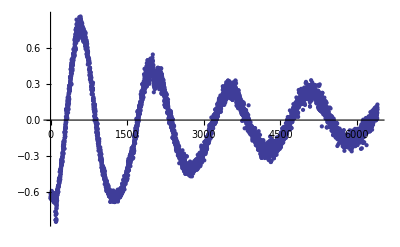

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
ExData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data]}];
ListPlot[ExData]
```

## Beide Funktionen

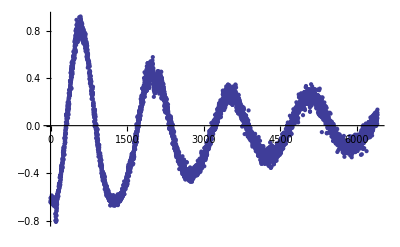

```mathematica
ListPlot[ExSymData]
```

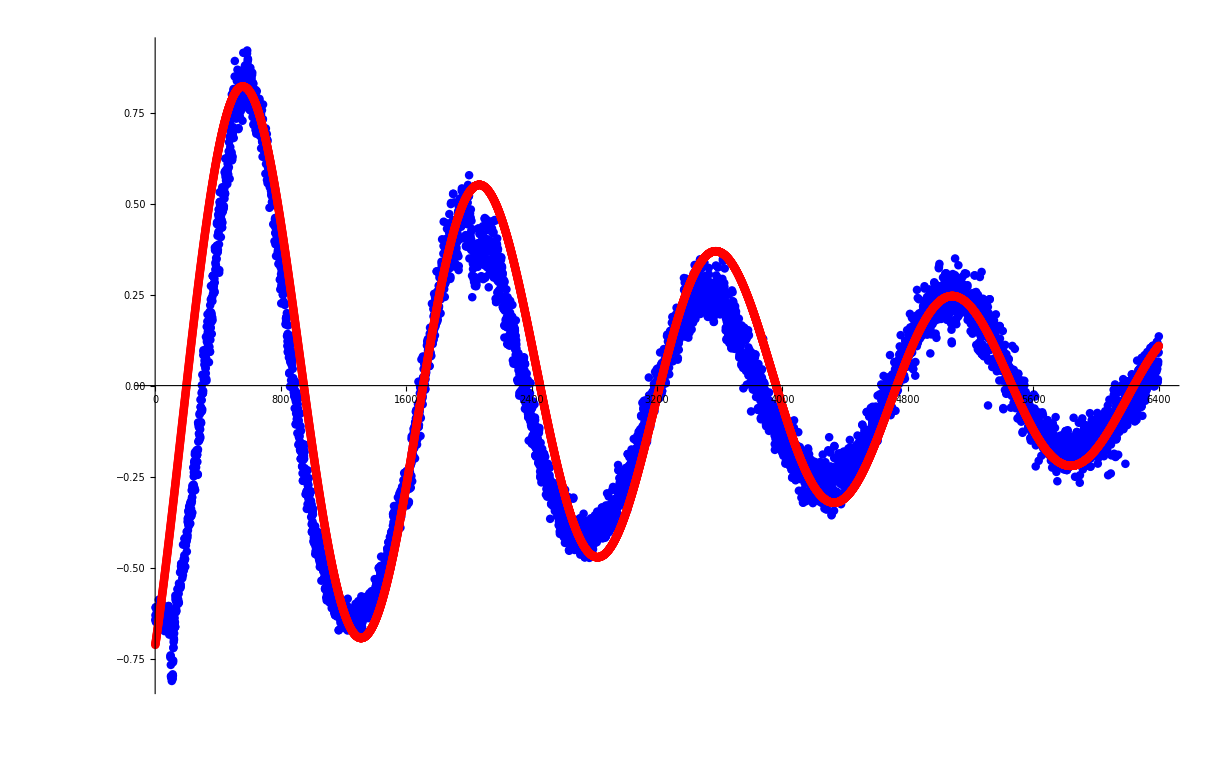

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.25; γct=240; j=1;shiftx=180;shifty=-0.01;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=ExSymData[[n]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=1.01*(-MzNormSpinDreh[Φ0/γct,c])+shifty,{Φ0,1+shift,Length[Data]+shift,j}];
ListPlot[{ExSymData,ThData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

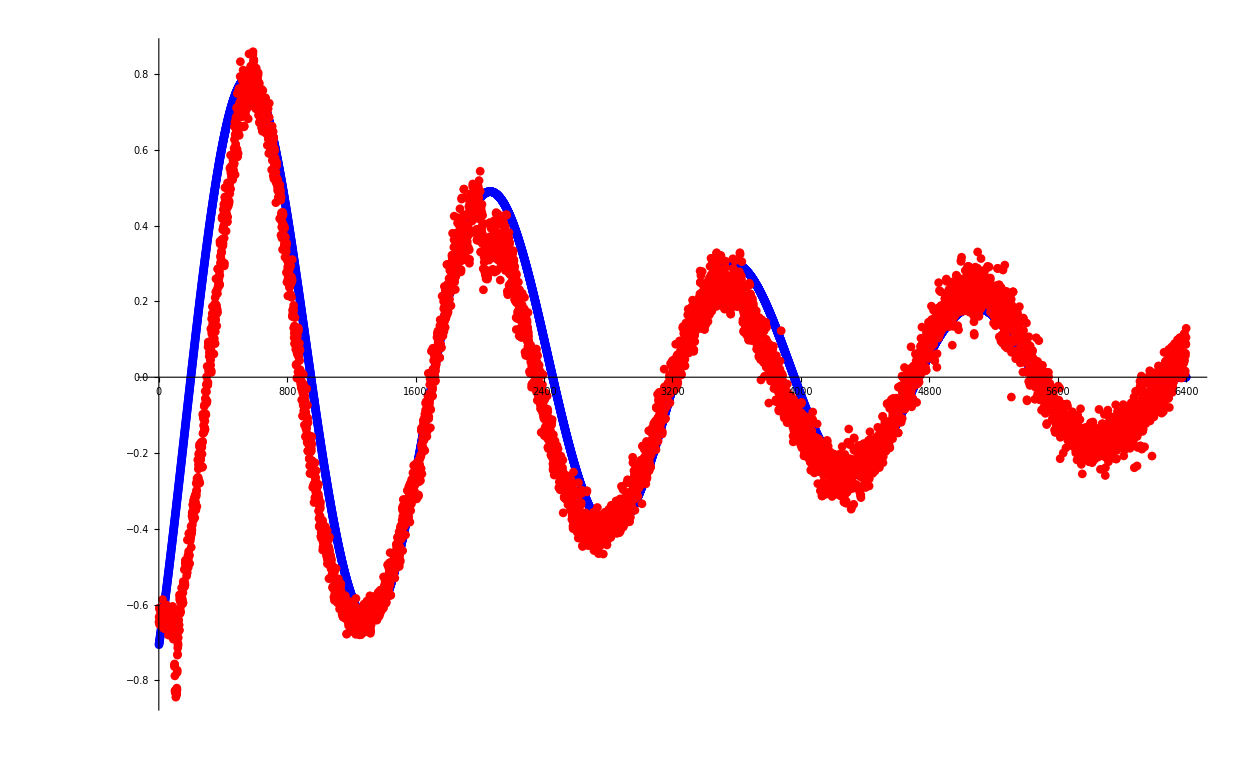

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.30; γct=240; j=1;shiftx=180;shifty=-0.01;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=1.01*(-MzNormSpinDreh[Φ0/γct,c])+shifty,{Φ0,1+shift,Length[Data],j}];
ListPlot[{ThData,ExData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

## Daten Exportieren

```mathematica
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\ThData_von_Mathematica.dat",ThData]
```

D:\Git\F-Praktikum\NMR\Data-Plots\ThData_von_Mathematica.dat

## Andere Versuche

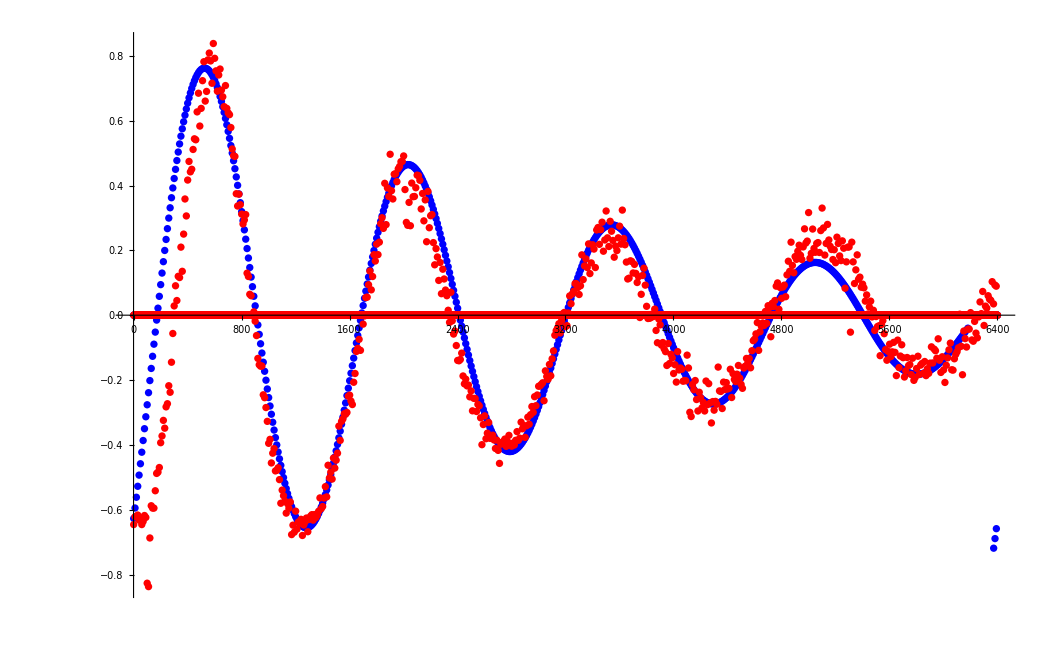

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.30; γct=240; j=10;shiftx=210;shifty=-0.03;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=-MzNormSpinDreh[Φ0/γct,c]+shifty,{Φ0,1+shift,Length[Data],j}];
ListPlot[{ThData,ExData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

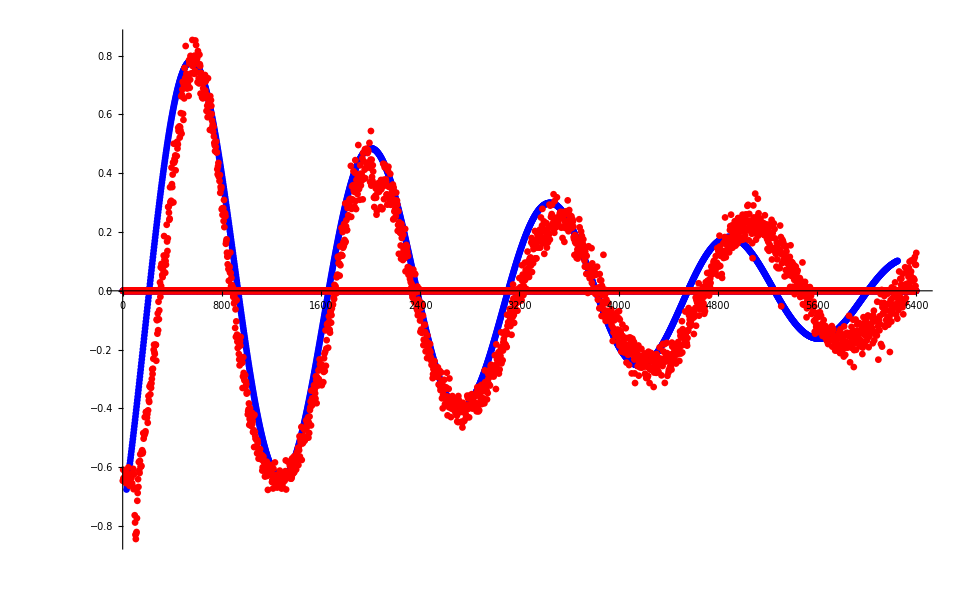

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.30; γct=230; j=30;shiftx=150;shifty=-0.01;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=-MzNormSpinDreh[Φ0/γct,c]+shifty,{Φ0,1+shift,Length[Data],j}];
ListPlot[{ThData,ExData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

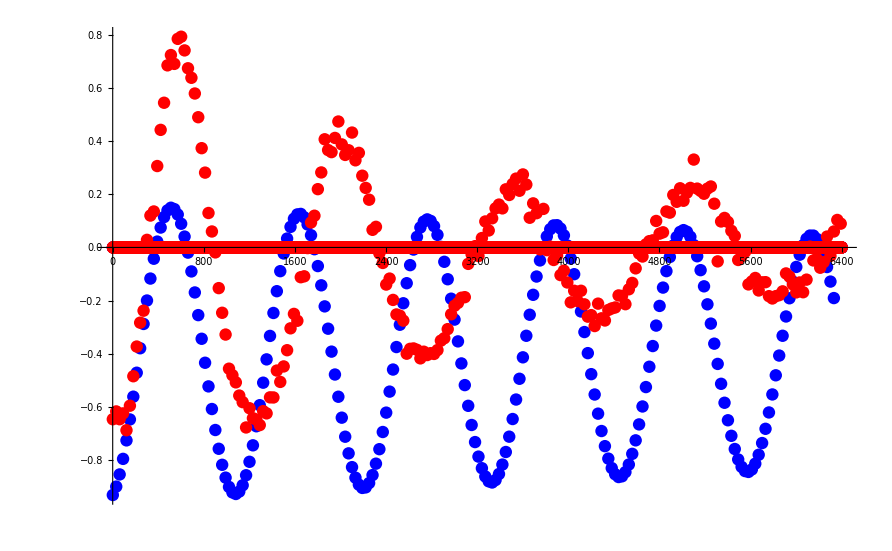

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
offres=0.8;
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[1/(1+offres)(offres+Cos[Φ *Sqrt[1+offres]])*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.02; γct=240; j=30;shiftx=45;shifty=0.05;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=-MzNormSpinDreh[Φ0/γct,c]+shifty,{Φ0,1+shiftx,Length[Data],j}];
ListPlot[{ThData,ExData},PlotStyle->{{Blue,PointSize[0.01]},{Red,PointSize[0.01]}}, PlotRange->Full]
```